```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2, 1/2<x≤3/2}, {c21(x-2)+c22(x-2)^2, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
C2r=Simplify[h[x],3/2<x≤5/2]/.x->3/2
C3l=Simplify[h[x],3/2<x≤5/2]/.x->5/2
```

1+c01/2+c02/4

1/2 (-c11+c12/2)

1/2 (c11+c12/2)

1/2 (-c21+c22/2)

1/2 (c21+c22/2)

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 (c12+c22)}

{0,-2 (c11+2 c21)}

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==C2r,
	C3l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[2]]==1
	},
	{c01,c02,c11,c12,c21,c22}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c11→-3/2-c02/2,c12→1,c21→1/2+c02/4,c22→-1-c02/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

1/16 (8 φ^2+8 y^2 (-1+φ) (1+c02-φ+c02 φ)+4 y (-1-2 (3+c02) φ+(3+c02) φ^2)+x (4+8 (3+c02) φ-4 (3+c02) φ^2+y (-1+φ) (28+52 φ+c02^2 (3+7 φ)+2 c02 (9+19 φ))+y^2 (8+16 φ-6 c02^2 (-2+φ) φ-8 φ^2+c02 (4+40 φ-20 φ^2)))+2 x^2 (3 c02^2 y ((-2+φ) φ+2 y (-1+φ^2))+2 c02 (2 (-1+φ^2)+2 y^2 (-3+2 φ+φ^2)+y (-1-10 φ+5 φ^2))+4 (-(-1+φ)^2+y (-1-2 φ+φ^2)+y^2 (-2-4 φ+6 φ^2))))
1/16 (2 (2+c02) x (1+2 x) (5+c02-2 y) (-1+y)+(2+c02)^2 x (1+2 x) (-1+y) (-3+2 y)-2 (2+c02) x (3+c02+2 x) (-1+y) (-3+2 y)+4 x (3+c02+2 x) (1+c02 (-1+y)^2) φ^2-4 (1+c02 x^2) (5+c02-2 y) (-1+y) φ^2+(2+c02) (3+c02-2 x) x (-1+y) (-3+2 y) φ^2-(2+c02) x (1+2 x) (-1+y) (1+c02+2 y) φ^2+2 (2+c02) x (1+2 x) (1+c02 (-1+y)^2) (-1-2 φ+φ^2)+2 x (3+c02+2 x) (5+c02-2 y) (-1+y) (-1-2 φ+φ^2)+2 (2+c02) (1+c02 x^2) (-1+y) (-3+2 y) (-1-2 φ+φ^2))
1/16 ((2+c02)^2 (3+5 x+2 x^2) (-1+y) (-3+2 y)-2 (2+c02) (3+5 x+2 x^2) (1+c02 (-1+y)^2) φ^2-2 (1+x) (5+c02+2 x) (5+c02-2 y) (-1+y) φ^2-2 (2+c02) (1+c02 (1+x)^2) (-1+y) (-3+2 y) φ^2-(2+c02) (3+5 x+2 x^2) (5+c02-2 y) (-1+y) (-1-2 φ+φ^2)+(2+c02) (1+x) (5+c02+2 x) (-1+y) (-3+2 y) (-1-2 φ+φ^2))
1/32 (2+c02) (-2+y) (2 (3+5 x+2 x^2) (7+c02-2 y) φ^2-2 (1+x) (5+c02+2 x) (-5+2 y) φ^2-(2+c02) (3+5 x+2 x^2) (-5+2 y) (-1-2 φ+φ^2))
1/32 (2+c02)^2 (10+9 x+2 x^2) (-2+y) (-5+2 y) φ^2
0

1/16 (-c02^2 (-1+x) y (-6-10 φ+13 φ^2+6 x (1+2 y (-2+φ) φ-φ^2)-6 y (1-4 φ+φ^2))-4 (2-4 φ-3 φ^2+y (8+20 φ-18 φ^2)+4 y^2 (1-4 φ+2 φ^2)+2 x^2 (-φ^2+2 y^2 φ (-4+3 φ)-y (-2+φ^2))-x (4-7 φ^2+y (8+20 φ-17 φ^2)+y^2 (4-32 φ+22 φ^2)))-2 c02 (y (14+28 φ-31 φ^2)+2 (1-4 φ+φ^2)-2 y^2 (-6+12 φ+φ^2)+2 x^2 (2 y^2 (-4+φ) φ+2 (-2+φ) φ+y (6-5 φ^2))+x (-2+16 φ-6 φ^2+2 y^2 (-6+16 φ+φ^2)+y (-24-28 φ+39 φ^2))))
1/16 (-c02^2 (-1+x) (1+y) (9+28 φ-24 φ^2-4 y (-3-3 φ+4 φ^2)+4 x (-3-3 φ+4 φ^2+y (-3+2 φ^2)))-2 c02 (-7-66 φ+41 φ^2+2 y^2 (-7-14 φ+12 φ^2)+y (-17-90 φ+60 φ^2)+x (17+90 φ-60 φ^2+y (31+122 φ-87 φ^2)+y^2 (22+36 φ-34 φ^2))+2 x^2 (-7-14 φ+12 φ^2+y^2 (-6-4 φ+6 φ^2)+y (-11-18 φ+17 φ^2)))+2 (-2+52 φ-13 φ^2+y^2 (8+6 φ^2)+y (-4+32 φ+9 φ^2)+2 x^2 (4+3 φ^2+y^2 (4-8 φ+6 φ^2)+y (6-12 φ+13 φ^2))-x (-4+32 φ+9 φ^2+2 y^2 (6-12 φ+13 φ^2)+y (2-20 φ+59 φ^2))))
1/16 (c02^2 (-2+x) (1+y) (-21+40 φ-12 φ^2-4 y (3-9 φ+4 φ^2)+4 x (2+y-5 φ-4 y φ+2 φ^2+2 y φ^2))+2 c02 (97-66 φ-29 φ^2+y (137-114 φ-33 φ^2)+y^2 (50-68 φ+6 φ^2)+2 x^2 (9-10 φ+y (12-16 φ+φ^2)+2 y^2 (2-4 φ+φ^2))+x (-83+70 φ+16 φ^2-2 y^2 (20-32 φ+5 φ^2)+y (-114+116 φ+15 φ^2)))-2 (x (65+74 φ-115 φ^2+y (69+154 φ-195 φ^2)+y^2 (22+44 φ-62 φ^2))+2 x^2 (-7-6 φ+11 φ^2+y^2 (-2-4 φ+6 φ^2)+y (-7-14 φ+19 φ^2))+4 (-22-22 φ+34 φ^2+2 y^2 (-4-6 φ+9 φ^2)+y (-23-44 φ+57 φ^2))))
1/32 (c02^2 (-2+x) (2+y) (y (16+8 φ-14 φ^2)+5 (6+8 φ-9 φ^2)+2 x (-8-4 φ+7 φ^2+2 y (-2+φ^2)))+4 c02 (-2+x) (2+y) (5+90 φ-70 φ^2+y (6+28 φ-24 φ^2)+x (-6-28 φ+24 φ^2+y (-4-8 φ+8 φ^2)))+4 (88-560 φ+380 φ^2+y^2 (8-96 φ+68 φ^2)+y (56-472 φ+326 φ^2)+2 x^2 (2+y) (2-8 (3+y) φ+(17+6 y) φ^2)-x (2+y) (28-236 φ+163 φ^2+y (4-80 φ+58 φ^2))))
1/32 (-4 c02 (21-13 x+2 x^2) (10+9 y+2 y^2) (-1+φ)^2-c02^2 (21-13 x+2 x^2) (10+9 y+2 y^2) (-1+φ)^2-4 (202+189 y+42 y^2-13 x (10+9 y+2 y^2) (-1+φ)^2+2 x^2 (10+9 y+2 y^2) (-1+φ)^2-420 φ-378 y φ-84 y^2 φ+210 φ^2+189 y φ^2+42 y^2 φ^2))
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
FullSimplify[D[SumF1a4,{{x,y}}]],
FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
FullSimplify[D[SumF1b4,{{x,y}}]],
FullSimplify[D[SumF1b5,{{x,y}}]]
}];
```

```mathematica
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1a4=Simplify[DSumF1a4/.φ->1/2];
DSumF1a5=Simplify[DSumF1a5/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
DSumF1b4=Simplify[DSumF1b4/.φ->1/2];
DSumF1b5=Simplify[DSumF1b5/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-2-1/2)^(-1-1/2) (DSumF1a5.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(3-1/2)^(4-1/2) (DSumF1b5.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5];
```

```mathematica
Err=Err1
DErr=FullSimplify[D[Err,c02]];
H=FullSimplify[D[Err,{{c02},2}]];
Sols=Solve[DErr==0,c02];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

(1360512+c02 (2161584+c02 (1188000+c02 (253708+20325 c02))))/368640

1 | 0.0996855 | True
2 | 1.58408-0.861657 ⅈ | False
3 | 1.58408+0.861657 ⅈ | False

```mathematica
RootReduce[Sols[[1]]]
```

{c02→Root[180132+198000 #1+63427 #1^2+6775 #1^3&,1]}

{c01→0.,c11→-0.721136,c12→1.,c21→0.110568,c22→-0.221136,c02→-1.55773}

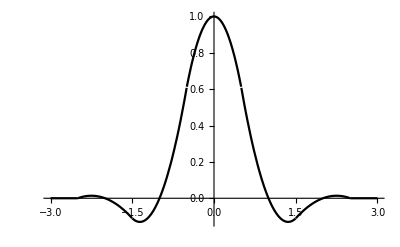

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```